# ListPlot

```mathematica
data = {{1,2},{3,4},{5,6}}
```

{{1,2},{3,4},{5,6}}

```mathematica
xdata = Transpose[data][[1]]
```

{1,3,5}

```mathematica
ydata = Transpose[data][[2]]
```

{2,4,6}

{1,2}

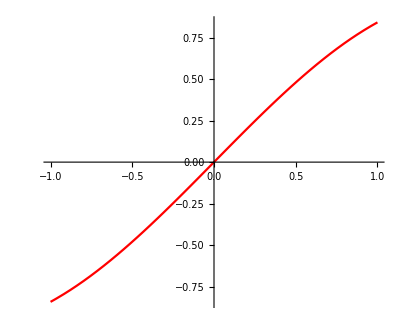

Interpolation::innd: First argument in xdata does not contain a list of data and coordinates.

Interpolation::innd: First argument in ydata does not contain a list of data and coordinates.

Show::gtype: ParametricPlotPlot is not a type of graphics.

```mathematica
{1,2}
fx := Interpolation[xdata]
fy:=Interpolation[ydata]


f55[t_]:={fx[t],fy[t]}

P1:= ParametricPlot[{t,Sin[t]},{t,-1,1},BaseStyle->{FontSize->14},PlotStyle->Red]

Show[P1]

Remove["Global`*"]
```